```mathematica
Quit[]
```

## RunMe()

```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
<<USMEFT`
```

## Zprime benchmarks points

```mathematica
benchmarksZp = {
(* 4 TeV *)
<|"MXX" -> 4, "β" -> 0.3|>,
<|"MXX" -> 4, "β" -> 0.5|>,
<|"MXX" -> 4, "β" -> 0.8|>,
<|"MXX" -> 4, "β" -> 1.0|>,
<|"MXX" -> 4, "β" -> 1.2|>,
(* 5 TeV *)
<|"MXX" -> 5, "β" -> 0.3|>,
<|"MXX" -> 5, "β" -> 0.5|>,
<|"MXX" -> 5, "β" -> 0.8|>,
<|"MXX" -> 5, "β" -> 1.0|>,
<|"MXX" -> 5, "β" -> 1.2|>,
<|"MXX" -> 5, "β" -> 1.5|>,
(* 6 TeV *)
<|"MXX" -> 6, "β" -> 0.3|>,
<|"MXX" -> 6, "β" -> 0.5|>,
<|"MXX" -> 6, "β" -> 0.8|>,
<|"MXX" -> 6, "β" -> 1.0|>,
<|"MXX" -> 6, "β" -> 1.2|>,
<|"MXX" -> 6, "β" -> 1.5|>,
(* 7 TeV *)
<|"MXX" -> 7, "β" -> 0.3|>,
<|"MXX" -> 7, "β" -> 0.5|>,
<|"MXX" -> 7, "β" -> 0.8|>,
<|"MXX" -> 7, "β" -> 1.0|>,
<|"MXX" -> 7, "β" -> 1.2|>,
<|"MXX" -> 7, "β" -> 1.5|>,
<|"MXX" -> 7, "β" -> 2.0|>,
(* 8 TeV *)
<|"MXX" -> 8, "β" -> 0.3|>,
<|"MXX" -> 8, "β" -> 0.5|>,
<|"MXX" -> 8, "β" -> 0.8|>,
<|"MXX" -> 8, "β" -> 1.0|>,
<|"MXX" -> 8, "β" -> 1.2|>,
<|"MXX" -> 8, "β" -> 1.5|>,
<|"MXX" -> 8, "β" -> 2.0|>
};
```

## Matching relations

### EW params

```mathematica
EWparam = {
g1 -> SMParam["ee"]/ SMParam["cθ"],
g2 -> SMParam["ee"]/ SMParam["sθ"],
vev -> SMParam["vev"],
Λ -> GetEFTScale[]
}
```

{g1→0.355976,g2→0.649553,vev→246.22,Λ→1000}

### Matching @ d=6

```mathematica
matchingZpd6 = {
WC["2JB"] -> -0.5 β^2 / MXX^2,
WC["ϕ,1"] -> 0.5 * g1^2 * β^2/MXX^2,
WC["BB"] -> 0.5 * g1^2 * β^2/MXX^2,
WC["BW"] -> 0.5 * g1 * g2 * β^2/MXX^2
};
```

```mathematica
(* !!!! MXX in TeV!!! *)
```

```mathematica
matchingZp["d6"] = Join[matchingZpd6 /. EWparam, {WC[name:Except["2JB"| "BW"| "ϕ,1"]] :> 0, "Λ" -> MXX}];
```

```mathematica
%//TableForm
```

c_(2JB)→-(0.5 β^2)/MXX^2
c_(ϕ,1)→(0.0633595 β^2)/MXX^2
c_BB→(0.0633595 β^2)/MXX^2
c_BW→(0.115613 β^2)/MXX^2
WC[name:Except[2JB|BW|ϕ,1]]:>0
Λ→MXX

### Matching @ (d=6)^2

```mathematica
overlineParams = {
WC["Δ4F"] -> WC["Δ4F"] * (1 - 2 vev^2/Λ^2 WC["WW"]),
WC["BW"] -> WC["BW"] * (1 - vev^2/Λ^2(WC["WW"] + WC["BB"])),
WC["2JB"] -> WC["2JB"] * (1 - 2 vev^2/Λ^2 WC["BB"])
};
```

```mathematica
(* Includes in the mathing the contribuiton of the d6 coefficients that are absorbed in the overline coefficients *)
```

```mathematica
matchingZp["d6sq"] = Join[WC[#] -> (WC[#] /. overlineParams/.matchingZp["d6"]/.EWparam) & /@ {"2JB", "ϕ,1", "BW"}, {WC[name:Except["2JB"| "BW"| "ϕ,1"]] :> 0,  "Λ" -> MXX}];
```

```mathematica
%//Simplify//TableForm
```

c_(2JB)→-(0.5 β^2 (MXX^2-0.00768223 β^2))/MXX^4
c_(ϕ,1)→(0.0633595 β^2)/MXX^2
c_BW→(0.115613 β^2 (MXX^2-0.00384112 β^2))/MXX^4
WC[name:Except[2JB|BW|ϕ,1]]:>0
Λ→MXX

### Matching @ d=8

```mathematica
overlineParamsd8 = {
WC["Δ4F"] -> WC["Δ4F"] - (g2^2 / 4 ) (vev/Λ)^2 WC["5ψ4H2"],
WC["2JB"] -> WC["2JB"] +(vev/Λ)^2 WC["4ψ4H2"],
WC["BW"] -> WC["BW"] + 1/2  (vev/Λ)^2(WC["1WBH4"] + g2/2 WC["1ψ2H4D"] + g1 WC["2ψ2H4D"]),
WC["ϕ,1"] -> WC["ϕ,1"] + (vev/Λ)^2 (WC["2H6"] - g1 WC["1ψ2H4D"] -   g2 (WC["2ψ2H4D"] - WC["4ψ2H4D"])),
WC["3W2H4"] -> WC["3W2H4"] + g2/2 (WC["2ψ2H4D"] - WC["4ψ2H4D"])
};
```

```mathematica
matchingZpd8 = {
WC["2H6"] -> -1/8 g2^2 g1^2 β^2 (1 + β^2)/MXX^4,
WC["2ψ2H4D"] -> -1/8  g2 g1^2  β^2 (1 + β^2)/MXX^4,
WC["2ψ4D2"] -> -1/2 β^2/MXX^4,
WC[name:Except["2H6"| "2ψ2H4D"|"2ψ4D2"]] :> 0
}
```

{c_(H^6)^(2)→-(g1^2 g2^2 β^2 (1+β^2))/(8 MXX^4),c_(ψ^2H^4D)^(2)→-(g1^2 g2 β^2 (1+β^2))/(8 MXX^4),c_(ψ^4D^2)^(2)→-β^2/(2 MXX^4),WC[name:Except[2H6|2ψ2H4D|2ψ4D2]]:>0}

```mathematica
matchingZp["d8"] = Join[WC[#] -> (WC[#] /.overlineParamsd8/. overlineParams/.matchingZpd6/.matchingZpd8/.EWparam) & /@ {"2JB", "ϕ,1", "BW", "3W2H4", "2ψ4D2"}, {WC[name:Except["2JB"| "BW"| "ϕ,1"| "2ψ4D2"|"3W2H4"]] :> 0,  "Λ" -> MXX}];
```

```mathematica
%//Expand//TableForm
```

c_(2JB)→-(0.5 β^2)/MXX^2+(0.00384112 β^4)/MXX^4
c_(ϕ,1)→(0.0633595 β^2)/MXX^2
c_BW→-(0.00011102 β^2)/MXX^4+(0.115613 β^2)/MXX^2-(0.000555102 β^4)/MXX^4
c_(W^2H^4)^(3)→-(0.00334158 β^2)/MXX^4-(0.00334158 β^4)/MXX^4
c_(ψ^4D^2)^(2)→-β^2/(2 MXX^4)
WC[name:Except[2JB|BW|ϕ,1|2ψ4D2|3W2H4]]:>0
Λ→MXX

## Loads benchmark and return χ2 function

```mathematica
Buildχ2[βparam_, MXXparam_,  OrderEFT_, OpDim_, matching_] := Module[
{
χ2ew, χ2lhc
},
(* Loads the pseudo-data for the NCDY channel *)
LoadZprimeBenchmark[βvalue -> βparam, mxxvalue -> MXXparam];
(* Updates the EWPO using the current benchmark points *)
LoadZprimeBenchmarkEW[matching, {β-> βparam, MXX -> MXXparam}, EFTOrder -> OrderEFT, OperatorDimension -> OpDim];
(* Builds χ2 *)
χ2ew = χ2EWPO[EFTOrder-> OrderEFT, OperatorDimension-> OpDim, MatchingRelations -> matching];
χ2lhc = χ2LHC[EFTOrder-> OrderEFT, OperatorDimension-> OpDim, MatchingRelations -> matching];

Return [χ2ew + χ2lhc]
]
```

## Fit

### Return best - fit value and 1σ limits

```mathematica
GetBestFit[χ2_, param_] := Module[
{
	min, x	
},
(* Find the best fit value for x = β^2 *)
min = Last@First@Last@Minimize[{χ2, param >= 0}, param] ;
Return[min]
]
```

```mathematica
ConfidenceIntervalβ[χ2_] := Module[
{
βinterval
},
βinterval = ConfidenceInterval[χ2, β, 0.68];
(* Only the absolute values *)
Select[βinterval, Last[#] > 0 &]
]
```

### Results for each benchmark

#### d=6

```mathematica
χ2["d6"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"χ2" -> Simplify[Buildχ2[#[["β"]],  #[["MXX"]], 2, 6, matchingZp["d6"]]]
}  & /@ benchmarksZp;
```

```mathematica
fit["d6"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"βfit" -> GetBestFit[#[["χ2"]]/.MXX -> #[["MXX"]], β],
"σβ" -> ConfidenceIntervalβ[#[["χ2"]]/.MXX -> #[["MXX"]]]
}  & /@ χ2["d6"];
```

#### (d=6)^2

```mathematica
χ2["d6sq"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"χ2" -> Simplify[Buildχ2[#[["β"]],  #[["MXX"]], 4, 6, matchingZp["d6sq"]]]
}  & /@ benchmarksZp;
```

```mathematica
fit["d6sq"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"βfit" -> GetBestFit[#[["χ2"]]/.MXX -> #[["MXX"]], β],
"σβ" -> ConfidenceIntervalβ[#[["χ2"]]/.MXX -> #[["MXX"]]]
}  & /@ χ2["d6sq"];
```

#### d=8

```mathematica
χ2["d8"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"χ2" -> Simplify[Buildχ2[#[["β"]],  #[["MXX"]], 4, 8, matchingZp["d8"]]]
}  & /@ benchmarksZp;
```

```mathematica
fit["d8"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"βfit" -> GetBestFit[#[["χ2"]]/.MXX -> #[["MXX"]], β],
"σβ" -> ConfidenceIntervalβ[#[["χ2"]]/.MXX -> #[["MXX"]]]
}  & /@ χ2["d8"];
```

## Plot

#### Load MaTeX

```mathematica
<<MaTeX`
```

```mathematica
tickWithLabels=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.02,.01}];

tickNoLabels[min_,max_]:=({#[[1]],"",#[[3]]}&/@tickWithLabels[min,max]);
```

```mathematica
ErrorBar[bestfit_, σs_] := Module[{
},
If[Length[σs] ===1,
{bestfit, σs[[1]][[2]] - bestfit  },
{bestfit - σs[[1]][[2]], σs[[2]][[2]] - bestfit  }
]
]
```

#### MXX = 4 TeV

```mathematica
results4TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 4 &];
```

```mathematica
results4TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 4 &];
```

```mathematica
results4TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 4 &];
```

```mathematica
M4TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results4TeV["d6"];
```

```mathematica
M4TeV["d6sq"] = {#[["β"]]+0.03,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results4TeV["d6sq"];
```

```mathematica
M4TeV["d8"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results4TeV["d8"];
```

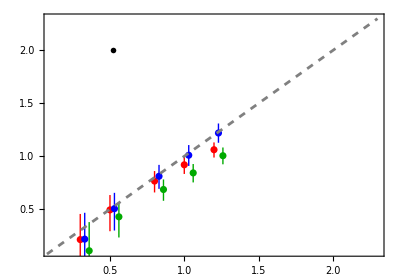

```mathematica
M4TeVPlot = Show[ListPlot[
{
M4TeV["d6"],
M4TeV["d6sq"],
M4TeV["d8"]
},
Frame->True,
PlotRange -> {{0.1,2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green]},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 4 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 5 TeV

```mathematica
results5TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 5 &];
```

```mathematica
results5TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 5 &];
```

```mathematica
results5TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 5 &];
```

```mathematica
M5TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results5TeV["d6"];
```

```mathematica
M5TeV["d6sq"] = {#[["β"]]+0.03,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results5TeV["d6sq"];
```

```mathematica
M5TeV["d8"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results5TeV["d8"];
```

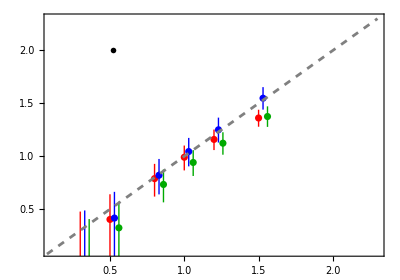

```mathematica
M5TeVPlot = Show[ListPlot[
{
M5TeV["d6"],
M5TeV["d6sq"],
M5TeV["d8"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1,2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green]},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 5 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 6 TeV

```mathematica
results6TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 6 &];
```

```mathematica
results6TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 6 &];
```

```mathematica
results6TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 6 &];
```

```mathematica
M6TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results6TeV["d6"];
```

```mathematica
M6TeV["d6sq"] = {#[["β"]]+0.03,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results6TeV["d6sq"];
```

```mathematica
M6TeV["d8"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results6TeV["d8"];
```

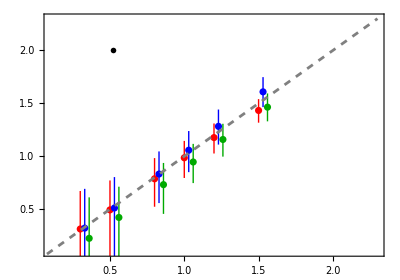

```mathematica
M6TeVPlot = Show[ListPlot[
{
M6TeV["d6"],
M6TeV["d6sq"],
M6TeV["d8"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green]},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 6 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 7 TeV

```mathematica
results7TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 7 &];
```

```mathematica
results7TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 7 &];
```

```mathematica
results7TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 7 &];
```

```mathematica
M7TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results7TeV["d6"];
```

```mathematica
M7TeV["d6sq"] = {#[["β"]]+0.03,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results7TeV["d6sq"];
```

```mathematica
M7TeV["d8"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results7TeV["d8"];
```

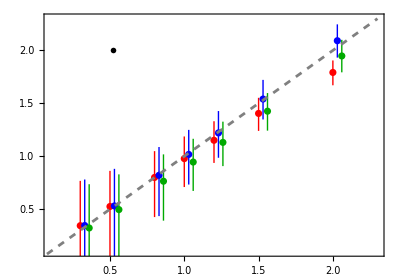

```mathematica
M7TeVPlot = Show[ListPlot[
{
M7TeV["d6"],
M7TeV["d6sq"],
M7TeV["d8"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green]},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 7 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 8 TeV

```mathematica
results8TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 8 &];
```

```mathematica
results8TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 8 &];
```

```mathematica
results8TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 8 &];
```

```mathematica
M8TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results8TeV["d6"];
```

```mathematica
M8TeV["d6sq"] = {#[["β"]]+0.03,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results8TeV["d6sq"];
```

```mathematica
M8TeV["d8"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results8TeV["d8"];
```

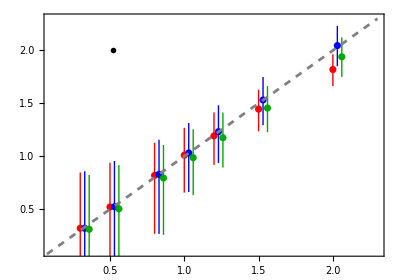

```mathematica
M8TeVPlot = Show[ListPlot[
{
M8TeV["d6"],
M8TeV["d6sq"],
M8TeV["d8"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green]},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 8 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### Grid plot

```mathematica
legend=SwatchLegend[{Red,Blue,Darker[Green]},{MaTeX["d = 6", FontSize->20],MaTeX["(d = 6)^2", FontSize->20],MaTeX["d = 8", FontSize->20]},LabelStyle->Directive[Black,5,FontFamily->"CMU Serif"],LegendLayout->"Column"]
```

```mathematica
legendPane=Pane[legend, Alignment->Center, ImageSize->{Automatic,75}  ];
```

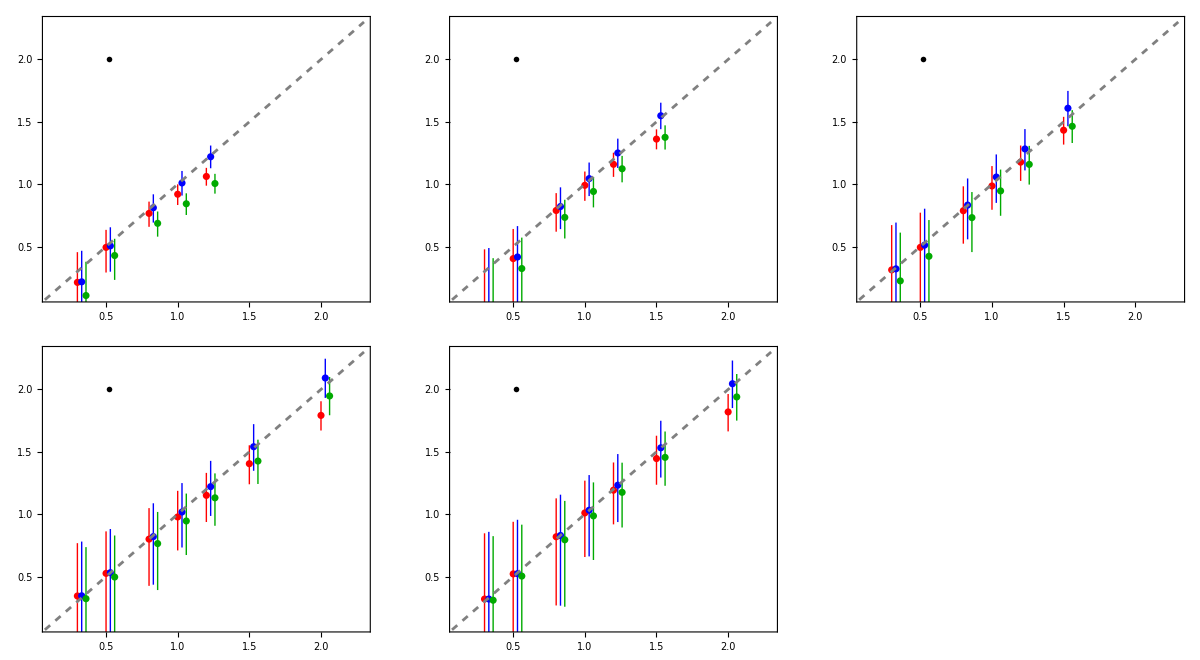

```mathematica
gridplt = GraphicsGrid[
{
{M4TeVPlot, M5TeVPlot, M6TeVPlot},
{M7TeVPlot, M8TeVPlot, legendPane}
},
Spacings->{5, 0.0},
ImageSize->1200
]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Export["FitZprimeMatching.pdf", gridplt]
```

FitZprimeMatching.pdf